```mathematica
(* uURc0[i,k] - перемещения (u) в направлении i от нагрузки, равномерно (U) распределенной в направлении k по прямоугольной a (по x1) на b (по x2)  области (R) в виде компилированных (c) с помощью CompilationTarget->"C" функций. Для использования требется Mathematica 8  и установленный компилятор С++ (Visual Studio), иначе надо удалить CompilationTarget->"C"*)
```

```mathematica
uURc0[1,1] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
1/(8 π μ (λ+2 μ))p0 (2 x3 (λ+2 μ) (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))])+2 x2 (λ+2 μ) (Log[x1+√(x1^2+x2^2+x3^2)]-Log[-a+x1+√((-a+x1)^2+x2^2+x3^2)])+(-x1 (λ+μ)+2 x1 (λ+2 μ)) (Log[x2+√(x1^2+x2^2+x3^2)]-Log[-b+x2+√(x1^2+(-b+x2)^2+x3^2)])+2 (-b+x2) (λ+2 μ) (-Log[x1+√(x1^2+(-b+x2)^2+x3^2)]+Log[-a+x1+√((-a+x1)^2+(-b+x2)^2+x3^2)])+((-a+x1) (λ+μ)-2 (-a+x1) (λ+2 μ)) (Log[x2+√((-a+x1)^2+x2^2+x3^2)]-Log[-b+x2+√((-a+x1)^2+(-b+x2)^2+x3^2)]))
],
CompilationTarget->"C"
];

uURc0[2,1] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
-(p0 (λ+μ))/(8 π μ (λ+2 μ)) (√(x1^2+x2^2+x3^2)-√((-a+x1)^2+x2^2+x3^2)-√(x1^2+(-b+x2)^2+x3^2)+√((-a+x1)^2+(-b+x2)^2+x3^2))
],
CompilationTarget->"C"
];
uURc0[3,1] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
-(p0 x3 (λ+μ))/(8 π μ (λ+2 μ)) (Log[x2+√(x1^2+x2^2+x3^2)]-Log[x2+√((-a+x1)^2+x2^2+x3^2)]-Log[-b+x2+√(x1^2+(-b+x2)^2+x3^2)]+Log[-b+x2+√((-a+x1)^2+(-b+x2)^2+x3^2)])
],
CompilationTarget->"C"
];

uURc0[1,2] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
-(p0 (λ+μ))/(8 π μ (λ+2 μ)) (√(x1^2+x2^2+x3^2)-√((-a+x1)^2+x2^2+x3^2)-√(x1^2+(-b+x2)^2+x3^2)+√((-a+x1)^2+(-b+x2)^2+x3^2)) 
],
CompilationTarget->"C"
];

uURc0[2,2] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(8 π μ (λ+2 μ))*(2 x3 (λ+2 μ) (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))])+(-x2 (λ+μ)+2 x2 (λ+2 μ)) (Log[x1+√(x1^2+x2^2+x3^2)]-Log[-a+x1+√((-a+x1)^2+x2^2+x3^2)])+2 x1 (λ+2 μ) (Log[x2+√(x1^2+x2^2+x3^2)]-Log[-b+x2+√(x1^2+(-b+x2)^2+x3^2)])+((-b+x2) (λ+μ)-2 (-b+x2) (λ+2 μ)) (Log[x1+√(x1^2+(-b+x2)^2+x3^2)]-Log[-a+x1+√((-a+x1)^2+(-b+x2)^2+x3^2)])+2 (-a+x1) (λ+2 μ) (-Log[x2+√((-a+x1)^2+x2^2+x3^2)]+Log[-b+x2+√((-a+x1)^2+(-b+x2)^2+x3^2)]))
],
CompilationTarget->"C"
];

uURc0[3,2] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
-(p0 x3 (λ+μ))/(8 π μ (λ+2 μ))*(Log[x1+√(x1^2+x2^2+x3^2)]-Log[-a+x1+√((-a+x1)^2+x2^2+x3^2)]-Log[x1+√(x1^2+(-b+x2)^2+x3^2)]+Log[-a+x1+√((-a+x1)^2+(-b+x2)^2+x3^2)])
],
CompilationTarget->"C"
];
uURc0[1,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
-(p0 x3 (λ+μ))/(8 π μ (λ+2 μ))*(Log[x2+√(x1^2+x2^2+x3^2)]-Log[x2+√((-a+x1)^2+x2^2+x3^2)]-Log[-b+x2+√(x1^2+(-b+x2)^2+x3^2)]+Log[-b+x2+√((-a+x1)^2+(-b+x2)^2+x3^2)])
],
CompilationTarget->"C"
];
uURc0[2,3] =  Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
-(p0 x3 (λ+μ))/(8 π μ (λ+2 μ))*(Log[x1+√(x1^2+x2^2+x3^2)]-Log[-a+x1+√((-a+x1)^2+x2^2+x3^2)]-Log[x1+√(x1^2+(-b+x2)^2+x3^2)]+Log[-a+x1+√((-a+x1)^2+(-b+x2)^2+x3^2)])
],
CompilationTarget->"C"
];

uURc0[3,3] =  Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];p0/(8 π μ (λ+2 μ))*(2 x3 μ (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))])+(λ+3 μ) (x2 (Log[x1+√(x1^2+x2^2+x3^2)]-Log[-a+x1+√((-a+x1)^2+x2^2+x3^2)])+x1 (Log[x2+√(x1^2+x2^2+x3^2)]-Log[-b+x2+√(x1^2+(-b+x2)^2+x3^2)])+(-b+x2) (-Log[x1+√(x1^2+(-b+x2)^2+x3^2)]+Log[-a+x1+√((-a+x1)^2+(-b+x2)^2+x3^2)])+(-a+x1) (-Log[x2+√((-a+x1)^2+x2^2+x3^2)]+Log[-b+x2+√((-a+x1)^2+(-b+x2)^2+x3^2)])))
],
CompilationTarget->"C"
];
```

```mathematica
(* sURc0[i,j,k] - напряжения (s) ij от нагрузки, равномерно (U) распределенной в направлении k по прямоугольной a (по x1) на b (по x2)  области (R) в виде компилированных (c) с помощью CompilationTarget->"C" функций. Для использования требется Mathematica 8  и установленный компилятор С++ (Visual Studio), иначе надо удалить CompilationTarget->"C"*)
```

```mathematica
sURc0[1,1,1] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ))* ( (λ+μ) ((x1^2 x2)/((x1^2+x3^2) √(x1^2+x2^2+x3^2))-((-a+x1)^2 x2)/(((-a+x1)^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-(x1^2 (-b+x2))/((x1^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-a+x1)^2 (-b+x2))/(((-a+x1)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+ (2 λ+3 μ) ( Log[x2+√(x1^2+x2^2+x3^2)]- Log[x2+√((-a+x1)^2+x2^2+x3^2)]- Log[-b+x2+√(x1^2+(-b+x2)^2+x3^2)]+Log[-b+x2+√((-a+x1)^2+(-b+x2)^2+x3^2)]))
],
CompilationTarget->"C"
];

sURc0[1,2,1] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
(p0*(λ+μ))/(4 π (λ+2 μ))*(-x1/(√(x1^2+x2^2+x3^2))+(-a+x1)/(√((a-x1)^2+x2^2+x3^2))+x1/(√(x1^2+(b-x2)^2+x3^2))+(a-x1)/(√((a-x1)^2+(b-x2)^2+x3^2))) +1/(4 π)p0 (Log[x1+√(x1^2+x2^2+x3^2)]-Log[-a+x1+√((a-x1)^2+x2^2+x3^2)]-Log[x1+√(x1^2+(b-x2)^2+x3^2)]+Log[-a+x1+√((a-x1)^2+(b-x2)^2+x3^2)])
],
CompilationTarget->"C"
];

sURc0[1,3,1] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
(p0 x3 (λ+μ))/(4 π (λ+2 μ))*((x1 x2)/((x1^2+x3^2) √(x1^2+x2^2+x3^2))+((a-x1) x2)/(((-a+x1)^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-(x1 (-b+x2))/((x1^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-a+x1) (-b+x2))/(((-a+x1)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+p0/(4 π)* (- ArcTan[((-a+x1) (-b+x2))/(x3 √((a-x1)^2+(b-x2)^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(b-x2)^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((a-x1)^2+x2^2+x3^2))]-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))])

],
CompilationTarget->"C"
];

sURc0[2,2,1] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
(p0  (λ+μ))/(8 π (λ+2 μ))*(-(2 x2)/(√(x1^2+x2^2+x3^2))+(2 x2)/(√((-a+x1)^2+x2^2+x3^2))+(2 (-b+x2))/(√(x1^2+(-b+x2)^2+x3^2))-(2 (-b+x2))/(√((-a+x1)^2+(-b+x2)^2+x3^2))) +(p0 λ)/(8 π (λ+2 μ)) (-Log[-x2+√(x1^2+x2^2+x3^2)]+Log[x2+√(x1^2+x2^2+x3^2)]+Log[-x2+√((-a+x1)^2+x2^2+x3^2)]-Log[x2+√((-a+x1)^2+x2^2+x3^2)]+Log[b-x2+√(x1^2+(-b+x2)^2+x3^2)]-Log[-b+x2+√(x1^2+(-b+x2)^2+x3^2)]- Log[b-x2+√((-a+x1)^2+(-b+x2)^2+x3^2)]+Log[-b+x2+√((-a+x1)^2+(-b+x2)^2+x3^2)])
],
CompilationTarget->"C"
];

sURc0[2,3,1] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
(p0 x3 (λ+μ))/(4 π (λ+2 μ))*(-1/(√(x1^2+x2^2+x3^2))+1/(√((-a+x1)^2+x2^2+x3^2))+1/(√(x1^2+(-b+x2)^2+x3^2))-1/(√((-a+x1)^2+(-b+x2)^2+x3^2)))
],
CompilationTarget->"C"
];

sURc0[3,3,1] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
(p0 (λ+μ))/(4 π (λ+2 μ))*((x2 x3^2)/((x1^2+x3^2) √(x1^2+x2^2+x3^2))-(x2 x3^2)/(((-a+x1)^2+x3^2) √((-a+x1)^2+x2^2+x3^2))+((b-x2) x3^2)/((x1^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-b+x2) x3^2)/(((-a+x1)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2))) +(p0 μ)/(4 π (λ+2 μ))*(-Log[x2+√(x1^2+x2^2+x3^2)]+Log[x2+√((-a+x1)^2+x2^2+x3^2)]+Log[-b+x2+√(x1^2+(-b+x2)^2+x3^2)]-Log[-b+x2+√((-a+x1)^2+(-b+x2)^2+x3^2)])

],
CompilationTarget->"C"
];

sURc0[1,1,2] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(8 π (λ+2 μ))*((λ+μ) (-(2 x1)/(√(x1^2+x2^2+x3^2))+(2 (-a+x1))/(√((-a+x1)^2+x2^2+x3^2))+(2 x1)/(√(x1^2+(-b+x2)^2+x3^2))-(2 (-a+x1))/(√((-a+x1)^2+(-b+x2)^2+x3^2)))+λ (-Log[-x1+√(x1^2+x2^2+x3^2)]+Log[x1+√(x1^2+x2^2+x3^2)]+Log[a-x1+√((-a+x1)^2+x2^2+x3^2)]-Log[-a+x1+√((-a+x1)^2+x2^2+x3^2)]+Log[-x1+√(x1^2+(-b+x2)^2+x3^2)]-Log[x1+√(x1^2+(-b+x2)^2+x3^2)]-Log[a-x1+√((-a+x1)^2+(-b+x2)^2+x3^2)]+Log[-a+x1+√((-a+x1)^2+(-b+x2)^2+x3^2)]))
],
CompilationTarget->"C"
];



sURc0[1,2,2] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];

p0/(4 π (λ+2 μ))*((λ+μ) (-x2/(√(x1^2+x2^2+x3^2))+x2/(√((-a+x1)^2+x2^2+x3^2))+(-b+x2)/(√(x1^2+(-b+x2)^2+x3^2))-(-b+x2)/(√((-a+x1)^2+(-b+x2)^2+x3^2)))+(λ+2 μ) (Log[x2+√(x1^2+x2^2+x3^2)]-Log[x2+√((-a+x1)^2+x2^2+x3^2)]-Log[-b+x2+√(x1^2+(-b+x2)^2+x3^2)]+Log[-b+x2+√((-a+x1)^2+(-b+x2)^2+x3^2)]))
],
CompilationTarget->"C"
];



sURc0[1,3,2] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
(p0 x3 (λ+μ))/(4 π (λ+2 μ))*(-1/(√(x1^2+x2^2+x3^2))+1/(√((-a+x1)^2+x2^2+x3^2))+1/(√(x1^2+(-b+x2)^2+x3^2))-1/(√((-a+x1)^2+(-b+x2)^2+x3^2))) 
],
CompilationTarget->"C"
];

sURc0[2,2,2] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ))*((λ+μ)*((x1 x2^2)/((x2^2+x3^2) √(x1^2+x2^2+x3^2))-((-a+x1) x2^2)/((x2^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-(x1 (-b+x2)^2)/(((-b+x2)^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-a+x1) (-b+x2)^2)/(((-b+x2)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+(2 λ+3 μ)*(Log[x1+√(x1^2+x2^2+x3^2)]-Log[-a+x1+√((-a+x1)^2+x2^2+x3^2)]-Log[x1+√(x1^2+(-b+x2)^2+x3^2)]+Log[-a+x1+√((-a+x1)^2+(-b+x2)^2+x3^2)]))
],
CompilationTarget->"C"
];

sURc0[2,3,2] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];

(p0 x3 (λ+μ))/(4 π (λ+2 μ))*((x1 x2)/((x2^2+x3^2) √(x1^2+x2^2+x3^2))+((a-x1) x2)/((x2^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-(x1 (-b+x2))/(((-b+x2)^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((a-x1) (b-x2))/(((-b+x2)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2))) +p0/(4 π)*(-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))])
],
CompilationTarget->"C"
];

sURc0[3,3,2] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ)) ( (λ+μ)*((x1 x3^2)/((x2^2+x3^2) √(x1^2+x2^2+x3^2))+((a-x1) x3^2)/((x2^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-(x1 x3^2)/(((-b+x2)^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-a+x1) x3^2)/(((-b+x2)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+μ*(- Log[x1+√(x1^2+x2^2+x3^2)]+Log[-a+x1+√((-a+x1)^2+x2^2+x3^2)]+Log[x1+√(x1^2+(-b+x2)^2+x3^2)]-Log[-a+x1+√((-a+x1)^2+(-b+x2)^2+x3^2)]))
],
CompilationTarget->"C"
];

sURc0[1,1,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ))*(x3 (λ+μ) ((x1 x2)/((x1^2+x3^2) √(x1^2+x2^2+x3^2))-((-a+x1) x2)/(((-a+x1)^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-(x1 (-b+x2))/((x1^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-a+x1) (-b+x2))/(((-a+x1)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+λ (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))]))
],
CompilationTarget->"C"
];


sURc0[1,2,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
(p0 x3 (λ+μ))/(4 π (λ+2 μ))*(-1/(√(x1^2+x2^2+x3^2))+1/(√((-a+x1)^2+x2^2+x3^2))+1/(√(x1^2+(-b+x2)^2+x3^2))-1/(√((-a+x1)^2+(-b+x2)^2+x3^2)))
],
CompilationTarget->"C"
];

sURc0[1,3,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ)) ((λ+μ)*((x2 x3^2)/((x1^2+x3^2) √(x1^2+x2^2+x3^2))-(x2 x3^2)/(((-a+x1)^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-((-b+x2) x3^2)/((x1^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-b+x2) x3^2)/(((-a+x1)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+μ (Log[x2+√(x1^2+x2^2+x3^2)]-Log[x2+√((-a+x1)^2+x2^2+x3^2)]-Log[-b+x2+√(x1^2+(-b+x2)^2+x3^2)]+Log[-b+x2+√((-a+x1)^2+(-b+x2)^2+x3^2)]))
],
CompilationTarget->"C"
];
sURc0[2,2,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ))*(x3 (λ+μ) ((x1 x2)/((x2^2+x3^2) √(x1^2+x2^2+x3^2))-((-a+x1) x2)/((x2^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-(x1 (-b+x2))/(((-b+x2)^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-a+x1) (-b+x2))/(((-b+x2)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+λ (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))]))
],
CompilationTarget->"C"
];


sURc0[2,3,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ))*((λ+μ) ((x1 x3^2)/((x2^2+x3^2) √(x1^2+x2^2+x3^2))-((-a+x1) x3^2)/((x2^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-(x1 x3^2)/(((-b+x2)^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-a+x1) x3^2)/(((-b+x2)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+μ (Log[x1+√(x1^2+x2^2+x3^2)]-Log[-a+x1+√((-a+x1)^2+x2^2+x3^2)]-Log[x1+√(x1^2+(-b+x2)^2+x3^2)]+Log[-a+x1+√((-a+x1)^2+(-b+x2)^2+x3^2)]))
],
CompilationTarget->"C"
];

sURc0[3,3,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
(p0 x3 (λ+μ))/(4 π (λ+2 μ)) (-(x1 x2 (x1^2+x2^2+2 x3^2))/((x1^2+x3^2) (x2^2+x3^2) √(x1^2+x2^2+x3^2))+((-a+x1) x2 ((-a+x1)^2+x2^2+2 x3^2))/(((-a+x1)^2+x3^2) (x2^2+x3^2) √((-a+x1)^2+x2^2+x3^2))+(x1 (-b+x2) (x1^2+(-b+x2)^2+2 x3^2))/((x1^2+x3^2) ((-b+x2)^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((a-x1) (-b+x2) ((-a+x1)^2+(-b+x2)^2+2 x3^2))/(((-a+x1)^2+x3^2) ((-b+x2)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+p0/(4 π) (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))])

],
CompilationTarget->"C"
];
```

```mathematica
ME=10^10;ν=0.3;λ=(ν ME)/((1+ν)(1-2ν));μ=ME/(2(1+ν)); dz=-0.1;
```

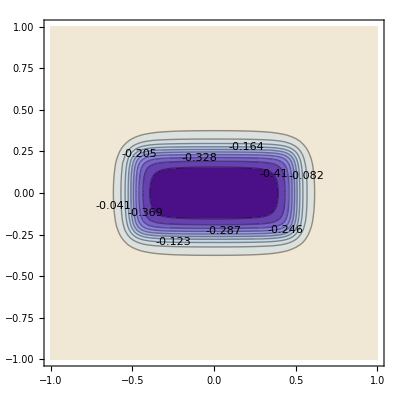

```mathematica
b=0.5;a=1; P0=-1;
bx=1;by=1;
Print[ContourPlot[sURc0[3,3,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

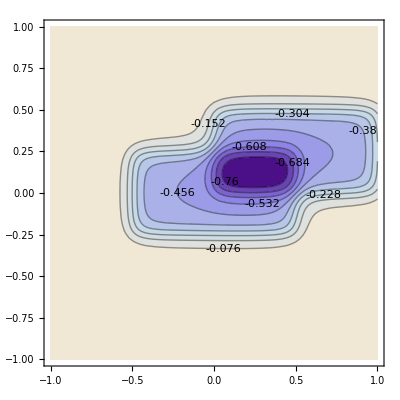

```mathematica
Print[ContourPlot[sURc0[3,3,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] +sURc0[3,3,3][x,a,y,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

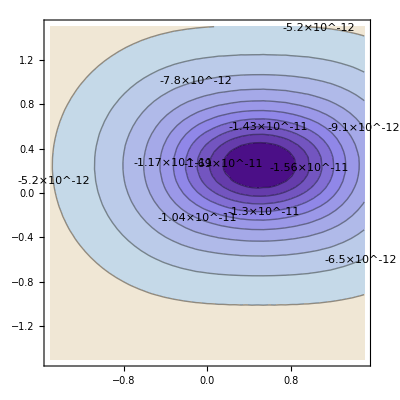

```mathematica
b=0.5;a=1; P0=-1;
bx=1.5;by=1.5;
Print[ContourPlot[uURc0[1,1][x,a,y,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

Force=1Component=1

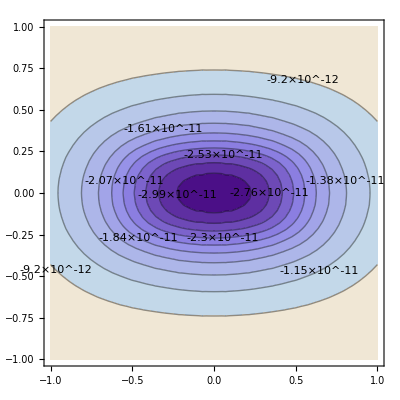

Force=1Component=2

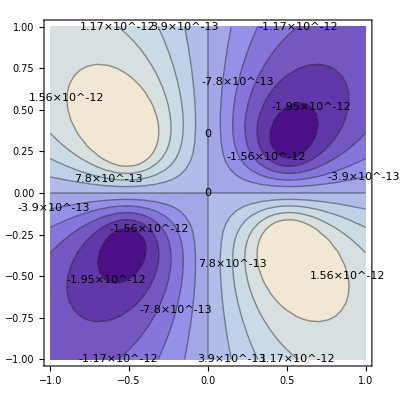

Force=1Component=3

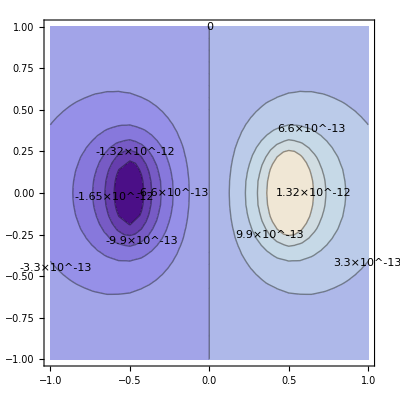

Force=2Component=1

-Graphics-

Force=2Component=2

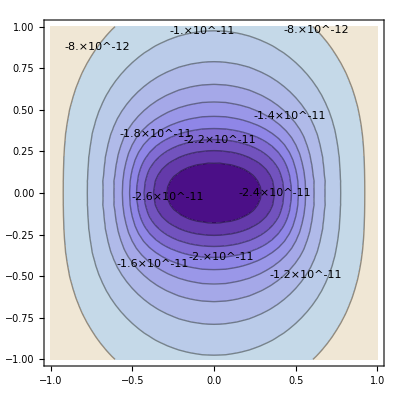

Force=2Component=3

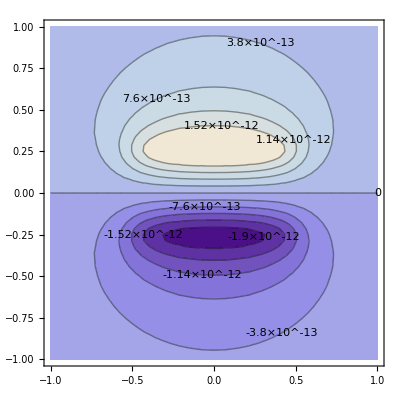

Force=3Component=1

-Graphics-

Force=3Component=2

-Graphics-

Force=3Component=3

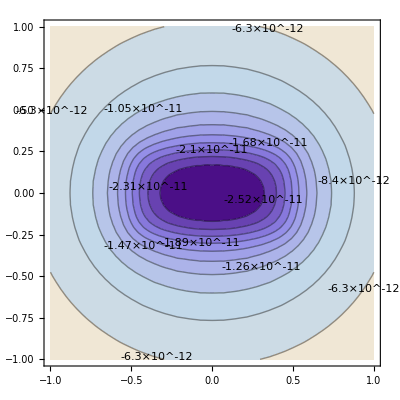

```mathematica
For[ii=1,ii≤3,ii++,
For[jj=1,jj≤3,jj++,
Print["Force=",ii,"Component=",jj];
Print[ContourPlot[uURc0[ii,jj][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];


]
]
```

```mathematica
x-a/2,a,y-b/2,b
```

Force=1Component=11

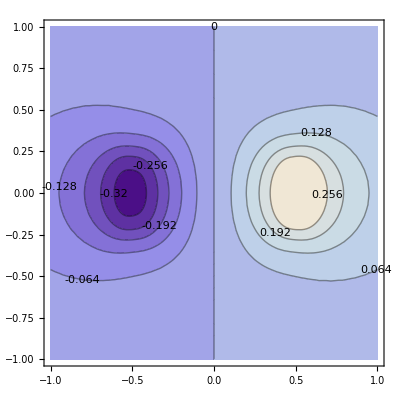

Force=1Component=12

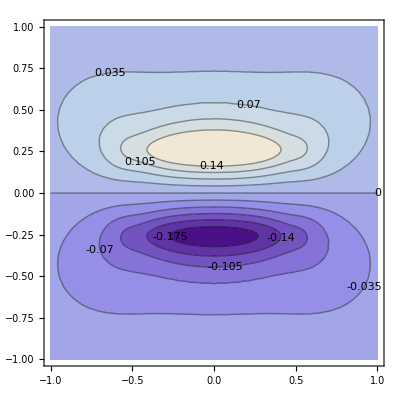

Force=1Component=13

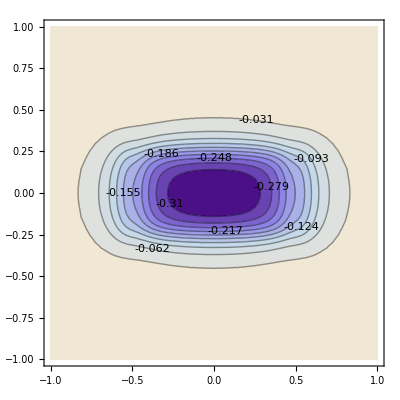

Force=1Component=21

-Graphics-

Force=1Component=22

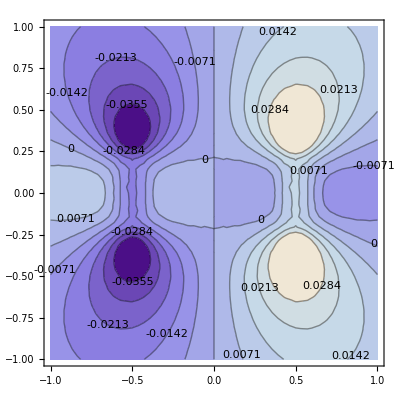

Force=1Component=23

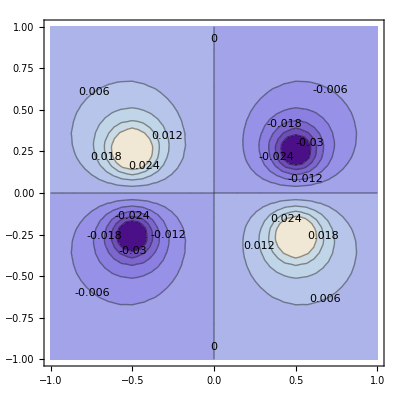

Force=1Component=31

-Graphics-

Force=1Component=32

-Graphics-

Force=1Component=33

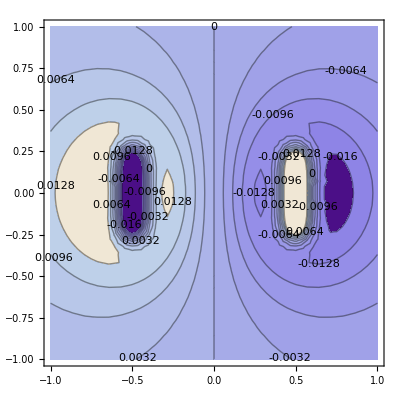

Force=2Component=11

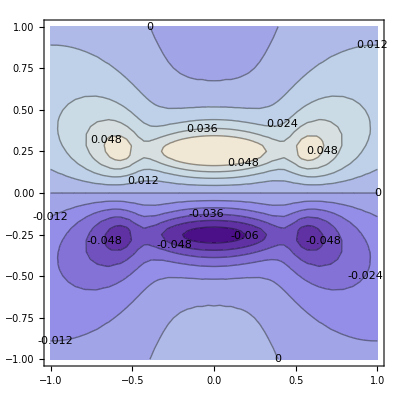

Force=2Component=12

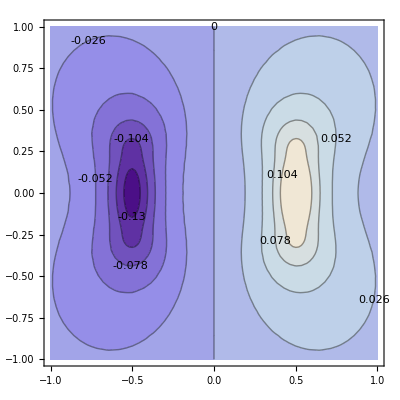

Force=2Component=13

-Graphics-

Force=2Component=21

-Graphics-

Force=2Component=22

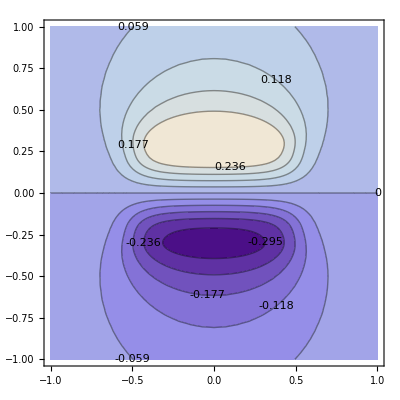

Force=2Component=23

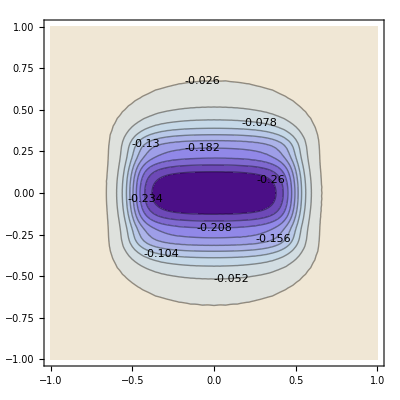

Force=2Component=31

-Graphics-

Force=2Component=32

-Graphics-

Force=2Component=33

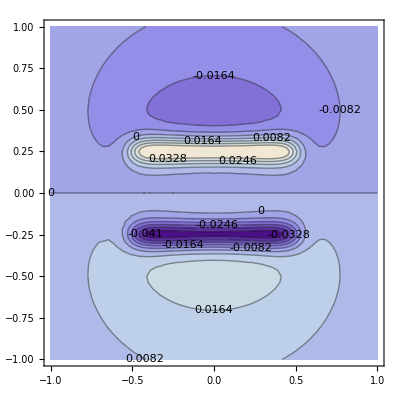

Force=3Component=11

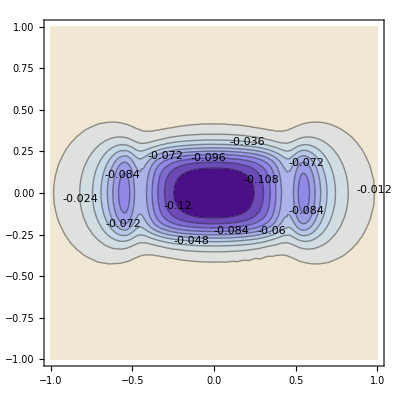

Force=3Component=12

-Graphics-

Force=3Component=13

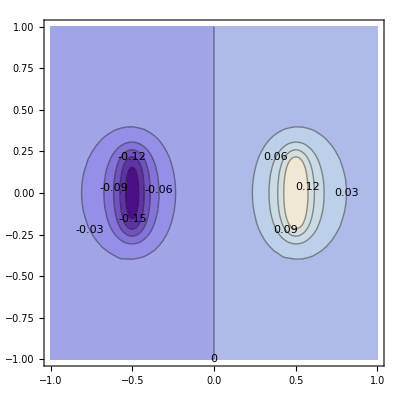

Force=3Component=21

-Graphics-

Force=3Component=22

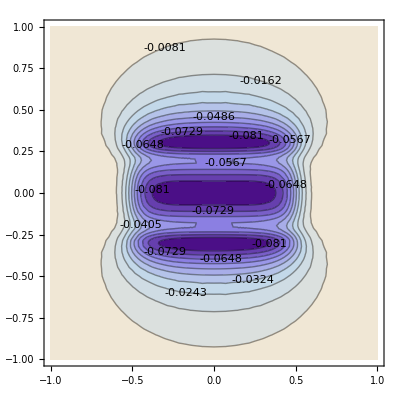

Force=3Component=23

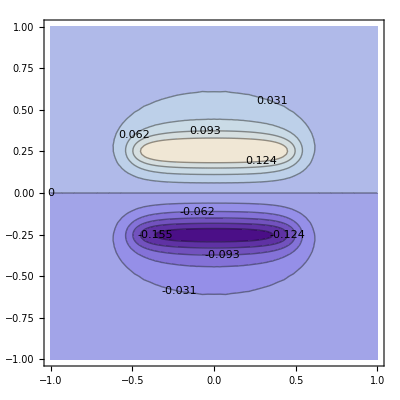

Force=3Component=31

-Graphics-

Force=3Component=32

-Graphics-

Force=3Component=33

-Graphics-

```mathematica
For[kk=1,kk≤3,kk++,
For[ii=1,ii≤3,ii++,
For[jj=1,jj≤3,jj++,
Print["Force=",kk,"Component=",ii,jj];
Print[ContourPlot[sURc0[ii,jj,kk][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];


]
]
]
```

```mathematica
uURc0[1,1]
```